```mathematica
ClearAll["Global`*"]
$Assumptions={k∈Reals,ω∈Complexes, c∈Reals,kx∈Reals,ky∈Reals,ρ0∈Reals,Ω∈Reals,ϵ∈Reals};
```

# Epsilons

```mathematica
matrixCoriolis:={{0,ρ0*kx,ρ0*ky},{kx/(ρ0*ϵ),0,ⅈ*2*Ω},{ky/(ρ0*ϵ),-ⅈ*2*Ω,0}}
```

```mathematica
evals=Eigenvalues[matrixCoriolis]//FullSimplify
```

{0,-(√(kx^2+ky^2+4 ϵ Ω^2))/(√ϵ),(√(kx^2+ky^2+4 ϵ Ω^2))/(√ϵ)}

```mathematica
TeXForm[(√(kx^2+ky^2+4 ϵ Ω^2))/(√ϵ)]
```

\frac{\sqrt{\text{kx}^2+\text{ky}^2+4 \Omega ^2 \epsilon }}{\sqrt{\epsilon }}

```mathematica
evals05=evals/.{Ω->0}//FullSimplify
```

{0,-(√(kx^2+ky^2))/(√ϵ),1/(√(ϵ/(kx^2+ky^2)))}

```mathematica
plotmanipulate=Manipulate[Plot3D[{0,-(√(kx^2+ky^2))/(√ϵ),1/(√(ϵ/(kx^2+ky^2)))},{kx,-5,5},{ky,-5,5},Mesh->None,PlotLegends->Automatic,AxesLabel->{kx,ky, ω},RegionFunction->Function[{x,y},x^2+y^2<25],ImageSize->Full,ColorFunction->(ColorData[{"TemperatureMap","Reverse"}][#3]&)],{ϵ,0.00001,15}]
```

```mathematica
plotting1={evals[[1]],evals[[2]],evals[[3]]}/.{kx->0,Ω->0.5,ϵ->1};
plotting075={evals[[1]],evals[[2]],evals[[3]]}/.{kx->0,Ω->0.5,ϵ->0.75};
plotting05={evals[[1]],evals[[2]],evals[[3]]}/.{kx->0,Ω->0.5,ϵ->0.5};
plotting025={evals[[1]],evals[[2]],evals[[3]]}/.{kx->0,Ω->0.5,ϵ->0.25};
plotting0={evals[[1]],evals[[2]],evals[[3]]}/.{kx->0,Ω->0.5,ϵ->0.0001};
plotting10={evals[[1]],evals[[2]],evals[[3]]}/.{kx->0,Ω->0.5,ϵ->10};
```

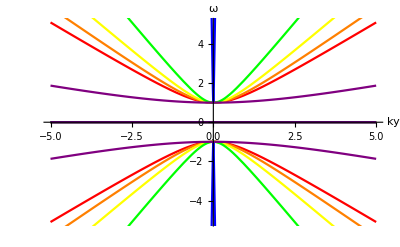

```mathematica
plot1=Plot[{plotting1},{ky,-5,5},Mesh->None,PlotStyle->Red,AxesLabel->{ky, ω},ImageSize->Full];
plot075=Plot[{plotting075},{ky,-5,5},Mesh->None,PlotStyle->Orange,AxesLabel->{ky, ω},ImageSize->Full];
plot05=Plot[{plotting05},{ky,-5,5},Mesh->None,PlotStyle->Yellow,AxesLabel->{ky, ω},ImageSize->Full];
plot025=Plot[{plotting025},{ky,-5,5},Mesh->None,PlotStyle->Green,AxesLabel->{ky, ω},ImageSize->Full];
plot0=Plot[{plotting0},{ky,-5,5},Mesh->None,PlotStyle->Blue,AxesLabel->{ky, ω},ImageSize->Full];
plot10=Plot[{plotting10},{ky,-5,5},Mesh->None,PlotStyle->Purple,AxesLabel->{ky, ω},ImageSize->Full];
plot=Show[plot1,plot075,plot05,plot025,plot0,plot10];
Needs["PlotLegends`"]
ShowLegend[plot,{{{Graphics[{Red,Line[{{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"ϵ=0.0001"}{0,0},{2,0}}]}],"ϵ=1"},{Graphics[{Orange,Line[{{0,0},{2,0}}]}],"ϵ=0.75"},{Graphics[{Yellow,Line[{{0,0},{2,0}}]}],"ϵ=0.5"},
{Graphics[{Green,Line[{{0,0},{2,0}}]}],"ϵ=0.25"},
{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"ϵ=0.0001"},{Graphics[{Purple,Line[{{0,0},{2,0}}]}],"ϵ=10"}},LegendPosition->{0.7,0.2},LegendSize->{0.45,0.4},LegendShadow->False}]
```

```mathematica
testplot={evals[[1]],evals[[2]],evals[[3]]}/.{Ω->6,ϵ->1};
test=Plot3D[testplot,{kx,-5,5},{ky,-5,5},Mesh->None,PlotLegends->Automatic,AxesLabel->{kx,ky, ω},RegionFunction->Function[{x,y},x^2+y^2<25],ImageSize->Full,ColorFunction->(ColorData[{"TemperatureMap","Reverse"}][#3]&)]
```

-Graphics3D-

{0,-√(1600+ky^2),√(1600+ky^2)}

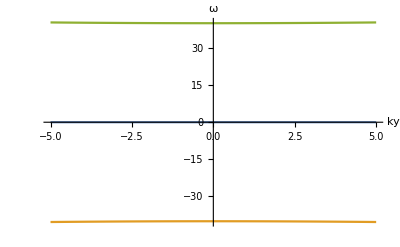

```mathematica
plottest={evals[[1]],evals[[2]],evals[[3]]}/.{Ω->20,kx->0,ϵ->1}
Plot[plottest,{ky,-5,5},Mesh->None,AxesLabel->{ky, ω},ImageSize->Full]
```